## Standard map

```mathematica
(*SetDirectory["C:\\Users\\MJGM_\\Documents\\animation"];*)
Clear[mapeo,lambda];
mapeo[Qini_,k_,n_]:=Module[{qold=Qini[[1]],pold=Qini[[2]],map,pnew,qnew},
map={};
AppendTo[map,Qini];

Do[
pnew=pold+k*Sin[qold]//N;
qnew=qold+pnew//N;
AppendTo[map,{qnew//N,pnew//N}];
{qold,pold}={qnew//N,pnew//N};

,{l,1,n}];

map

];

lambda[qini_,k_,e_,n_]:=Module[{dq=RandomPoint[Disk[qini,e],1][[1]],alfas,lambdas,delta,alfa,qnew,dqnew,l,list=mapeo[qini,k,n],list2,ratio},
list2=mapeo[dq,k,n];
ratio={};
lambdas={};

Do[
AppendTo[ratio,Norm[list[[i]]-list2[[i]]]/Norm[list[[1]]-list2[[1]]]];
,{i,1,Length[list]}];

Do[
l=(1/i)Sum[Log[ratio[[j]]/ratio[[j-1]]],{j,2,i}];
AppendTo[lambdas,l];
,{i,1,Length[list]}];

lambdas

];
```

```mathematica
ratio=Range[1,1000,0.5];
AppendTo[ratio,1001];
lambdas={};
Do[
l=(1/i)Sum[ratio[[j]]/ratio[[j-1]],{j,2,i+1}];
AppendTo[lambdas,l];
,{i,1,1000}];
lambdas//ListLogLogPlot
```

### Exponente de Lyapunov

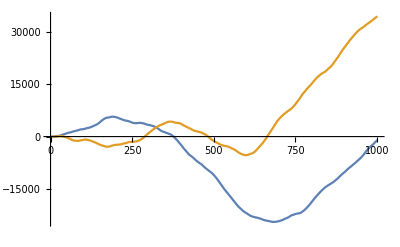

```mathematica
Clear[k,n,num,qini,a,b];
(*PUNTO INICIAL*)
q0={{3,0},{3-10^-6,0}};
n=1000;
k=10;
Table[mapeo[i,k,n][[All,1]],{i,q0}]//ListLinePlot
```

```mathematica
Clear[n,num,qini,a,b];
(*PUNTO INICIAL*)
q0=RandomPoint[Disk[],1][[1]];
n=1000;
num=10;

a=RandomReal[NormalDistribution[q0[[1]],10^-6],num];
b=Table[0,{i,1,num}];
qini=Transpose[{a,b}];

(*plots1={};
Do[
poincare=ParallelTable[mapeo3[i,j,n],{i,qini}];
puntos=ListPlot[poincare,ImageSize->600,PlotTheme->"Scientific",PlotRange->All,AspectRatio->1,PlotStyle->PointSize[0.003],PlotStyle->Black,PlotLabel->{Style["Q_0="<>ToString[q0],25],Style["k="<>ToString[j],25],Style["n="<>ToString[n],25]}];
disco=Graphics[{Thick,Circle[{0,0},1.999]},AspectRatio->1];
plot=Show[puntos,disco,PlotRange->All];
AppendTo[plots1,plot];
,{j,1.8,2.8,0.05}];*)
```

```mathematica
plots2={};
plots3={};
Do[
data=ParallelTable[Quiet[lambda[qini[[i]],j,10^-6,n]],{i,num}];
plot=ListLogLogPlot[Mean[data],PlotRange->All,PlotTheme->"Scientific",AspectRatio->1/2,ImageSize->1000,Joined->True,FrameLabel->{Style["n",20],Style[L,20]},PlotLabel->{Style["Q_0="<>ToString[q0],25],Style["k="<>ToString[j],25],Style["n="<>ToString[n],25]}];
AppendTo[plots2,plot];
AppendTo[plots3,{j,Mean[data][[-1]]}];

,{j,5,10,1}];
```

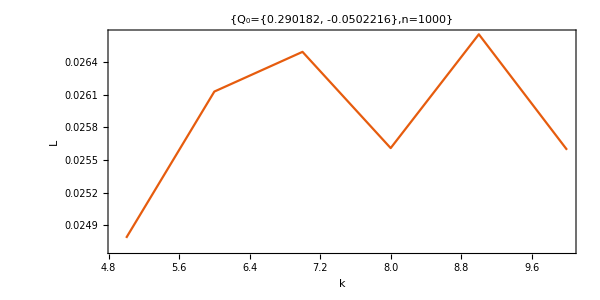

```mathematica
(*movie1=ListAnimate[plots1,AnimationRunning->False,AnimationRate->1]*)
movie2=ListAnimate[plots2,AnimationRunning->False,AnimationRate->1]
plot3=ListPlot[plots3,PlotRange->All,PlotTheme->"Scientific",AspectRatio->1/2,ImageSize->600,Joined->True,FrameLabel->{Style["k",20],Style[L,20]},PlotLabel->{Style["Q_0="<>ToString[q0],25],Style["n="<>ToString[n],25]}]
```

```mathematica
Export["moviea001.png",plots1,"VideoFrames"];
Export["movieb001.png",plots2,"VideoFrames"];
Export["plot.png",plot];
```

## Variables J mapeo 1

### Definiciones

```mathematica
Clear[mapeoJ,M,jmas,jmas2];

randompoint[cota_]:=randompoint[cota]=Module[{a=RandomPoint[Sphere[],50000],J0},

J0={};

Do[
If[a[[i,1]]^2+a[[i,3]]^2<=cota,
AppendTo[J0,Abs[a[[i]]]];
];

,{i,1,Length[a]}];
J0

];

Jx[x_,y_,z_,A_,B_]:=Jx[x,y,z,A,B]=x*Cos[A*(y*Sin[B]+z*Cos[B])]-y*Sin[A*(y*Sin[B]+z*Cos[B])]*Cos[B]+z*Sin[A*(y*Sin[B]+z*Cos[B])]*Sin[B];
Jy[x_,y_,z_,A_,B_]:=Jy[x,y,z,A,B]=x*Sin[A*(y*Sin[B]+z*Cos[B])]-y*Cos[A*(y*Sin[B]+z*Cos[B])]*Cos[B]-z*Cos[A*(y*Sin[B]+z*Cos[B])]*Sin[B];
Jz[x_,y_,z_,A_,B_]:=Jz[x,y,z,A,B]=y*Sin[B]+z*Cos[B];

M[Jini_,A_Real,B_Real]:=M[Jini,A,B]=Module[{M},
M={{D[Jx[x,y,z,A,B], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,A,B], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,A,B], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},
{D[Jy[x,y,z,A,B], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,A,B], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,A,B], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},{D[Jz[x,y,z,A,B], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,A,B], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,A,B], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}}}//N;
M
];

(*jmas[Jini_,A_Real,n_Integer]:=Module[{j,list=mapeoJ[N[Jini],N[A],n],data,B=N[Pi/2]},
data=Table[N[M[list[[i]],A,B]],{i,1,n}];
j=N[Log[Max[N[Abs[N[Eigenvalues[N[Fold[Dot,data]]]]]]]^(N[1/n])]]

];*)

ConvergencePlot[x_List] := Show[ Map[ListPlot[#, Joined -> True,DisplayFunction -> Identity, PlotRange -> All,ImageSize->600]&,Transpose[x] ],
    Frame -> True, FrameLabel -> {"Steps", "LCEs"},DisplayFunction -> $DisplayFunction];

mapeoJ[Jini_,A_Real,n_Integer]:=Module[{Ji=Jini,J,Jxnew,Jynew,Jznew,B=N[Pi/2]},

J={};
AppendTo[J,Ji];

Do[
Jznew=Ji[[2]]*N[Sin[B]]+Ji[[3]]*N[Cos[B]];
Jxnew=N[Ji[[1]]*N[Cos[A*Jznew]]-Ji[[2]]*N[Sin[A*Jznew]]*N[Cos[B]]+Ji[[3]]*N[Sin[A*Jznew]]*N[Sin[B]]];
Jynew=Ji[[1]]*N[Sin[A*Jznew]]-Ji[[2]]*N[Cos[A*Jznew]]*Cos[B]-Ji[[3]]*N[Cos[A*Jznew]]*N[Sin[B]];
Ji={Jxnew,Jynew,Jznew};
AppendTo[J,Ji];

,{i,1,n}];

J

];


mapeoJ2[Jini_,A_Real,n_Integer]:=Module[{Ji=Jini,J,Jxnew,Jynew,Jznew},
Do[
Jznew=Ji[[2]];
Jxnew=N[Ji[[1]]*N[Cos[A*Jznew]]+Ji[[3]]*N[Sin[A*Jznew]]];
Jynew=Ji[[1]]*N[Sin[A*Jznew]]-Ji[[3]]*N[Cos[A*Jznew]];
Ji={Jxnew,Jynew,Jznew};

,{i,n}];

Ji

];

jmas[Jini_,A_Real,n_Integer]:=Module[{j,list=mapeoJ[N[Jini],A,n],data,B=N[Pi/2]},
data=Table[N[M[list[[i]],A,B]],{i,1,n}];
j=N[Log[Max[Re[N[Eigenvalues[N[Fold[Dot,data]]]]]]^(N[1/n])]]

];

jmas2[Jini_,A_Real,n_Integer]:=Module[{xt,q,r,s,B=N[Pi/2],lces,tras=1},
xt=mapeoJ2[N[Jini],A,tras];
{q,r}=QRDecomposition[M[Jini,A,B]];
s={};

Do[
xt=mapeoJ2[xt,A,1];
{q,r}=QRDecomposition[M[xt,A,B].Transpose[q]];
(*s=Append[s,Table[r[[i,i]],{i,3}]];*)
s=Append[s,r[[1,1]]];

,{n}];

lces=Rest[FoldList[Plus,0,Re[Log[s]]]]/Range[n];
lces=lces[[2;;n]]
];
```

$Aborted

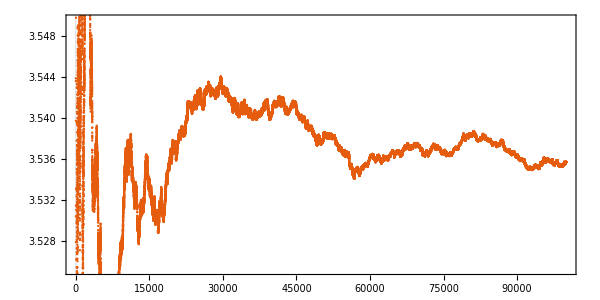

```mathematica
Clear[A,Ji];
(*Ji=RandomPoint[Sphere[],1][[1]];*)
Ji={0.45,-0.7,Sqrt[1-0.45^2-0.7^2]};
A=91.98;
(*tras=2000*)
n=150000;
data=jmas2[Ji,A,n];
plot1=ListPlot[data,AspectRatio->1/2,PlotTheme->"Scientific",ImageSize->600]
```

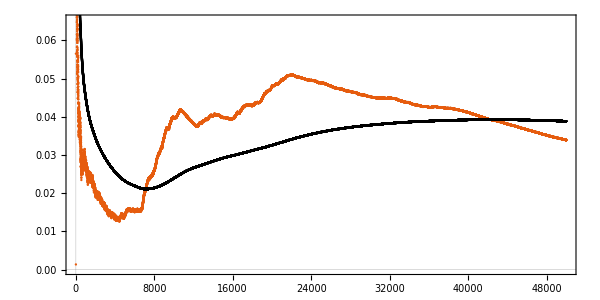

```mathematica
mean={};
std={};
Do[
data1=data[[1;;i]];
AppendTo[mean,Mean[data1]];
AppendTo[std,StandardDeviation[data1]];
,{i,2,Length[data]}];
plot2=ListPlot[mean,AspectRatio->1/2,PlotTheme->"Scientific",ImageSize->600,PlotStyle->Black];
plot3=ListPlot[std,AspectRatio->1/2,PlotTheme->"Scientific",ImageSize->600,PlotStyle->Blue];
Show[plot1,plot2]
```

```mathematica
Clear[A,Jini,data,plot1];
Ji=RandomPoint[Sphere[],1][[1]];
(*Ji={0.45,-0.7,Sqrt[1-0.45^2-0.7^2]};*)
n=5000;

data=ParallelTable[{i,Mean[jmas2[Ji,i,n]]},{i,1.0,50.0,N[Pi/2]}];
```

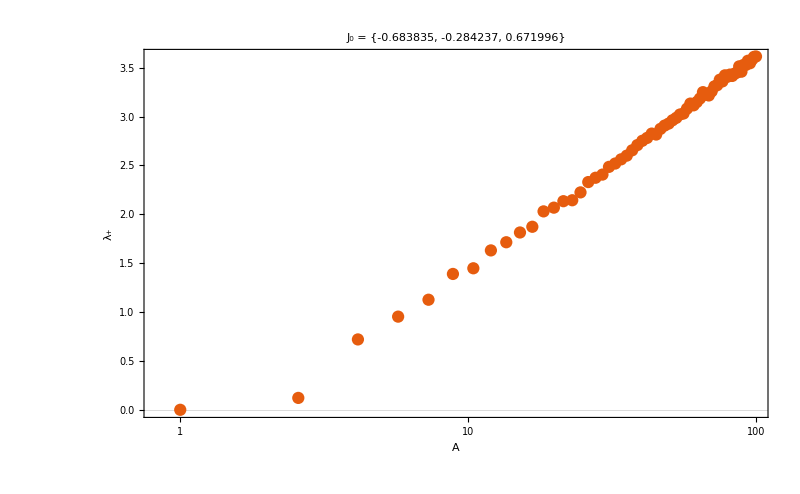

```mathematica
plot1=ListLogLinearPlot[data,PlotRange->All,PlotTheme->"Scientific",Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["A",40],Style["λ_+",40]},PlotLabel->Style["J_0 = "<>ToString[Ji],30], ImageSize->800]
```

```mathematica
data2=ParallelTable[{i,Mean[jmas[Ji,i,n]]},{i,1.0,100.0,N[Pi/2]}];
plot2=ListLogLinearPlot[data2,PlotRange->All,PlotTheme->"Scientific",Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["A",40],Style["λ_+",40]},PlotLabel->Style["J_0 = "<>ToString[Ji],30], ImageSize->800]
```

### Seccion de Poincare

```mathematica
Clear[J0,A,n,poincare,plot,esfera];
esfera=Graphics3D[{Opacity[0.3],Sphere[]},BoxRatios->1];
punto=Graphics3D[{PointSize[0.03],Point[{0.45,-0.7,Sqrt[1-0.45^2-0.7^2]}]}];
(*J0={0.45,-0.7,Sqrt[1-0.45^2-0.7^2]};*)
J0=RandomPoint[Sphere[],50];
A=1.80;
n=4000;

poincare=ParallelTable[mapeoJ[i,A,n],{i,J0}];
(*poincare=mapeoJ[J0,A,n];*)
```

```mathematica
plot=ListPointPlot3D[poincare,ImageSize->900,PlotTheme->"Scientific",PlotRange->All,BoxRatios->1,PlotStyle->PointSize[0.003],AxesLabel->{Style["X",40],Style["Y",40],Style["Z",40]},PlotLabel->Style["A="<>ToString[A],25]];
Show[plot,esfera]
```

```mathematica
Clear[J0,A,B,n,poincare,plot,esfera];
a=RandomPoint[Sphere[],20000];
J0={};
Do[
If[a[[i,2]]^2+a[[i,3]]^2<=0.001,
AppendTo[J0,Abs[a[[i]]]];
];

,{i,1,Length[a]}];
A=6.05;
n=1000;

poincare=ParallelTable[mapeoJ[i,A,n],{i,J0}];
```

```mathematica
plot=ListPointPlot3D[poincare,ImageSize->600,PlotTheme->"Scientific",PlotRange->All,BoxRatios->1,PlotStyle->PointSize[0.005]];
esfera=Graphics3D[{Opacity[0.3],Sphere[]},BoxRatios->1];
Show[plot,esfera]
```

-Graphics3D-

### Seccion de Poincare y proyeccion en t

```mathematica
Clear[J0,A,B,n,poincare,plot,esfera];
esfera=Graphics3D[{Opacity[0.3],Sphere[]},BoxRatios->1];
punto=Graphics3D[{PointSize[0.01],Point[{0.45,-0.7,Sqrt[1-0.45^2-0.7^2]}]}];
J1={0,0,1};
J2={0,-1,0};
J3={0,0,-1};
J4={0,1,0};
J0={0.45,-0.7,Sqrt[1-0.45^2-0.7^2]};
(*J0=RandomPoint[Sphere[],50];*)
n=15000;

movie={};
Do[

poincare=mapeoJ[J0,i,n];
plot=ListPointPlot3D[poincare,ImageSize->800,PlotTheme->"Scientific",PlotRange->All,BoxRatios->1,PlotStyle->PointSize[0.003],AxesLabel->{"x","y","z"},PlotLabel->{Style["J_0="<>ToString[J0],25],Style["A="<>ToString[i],25]}];
AppendTo[movie,Show[plot,esfera]];

,{i,0,3Pi,Pi/50.}];
```

```mathematica
ListAnimate[movie,AnimationRunning->False]
```

```mathematica
Clear[J0,B,n,poincare,plot,disco,projection];
disco=Graphics[{Circle[]}];
J0={0.45,-0.7,Sqrt[1-0.45^2-0.7^2]};
(*J0=RandomPoint[Sphere[],50];*)
n=1000;

movie={};
Do[
poincare=mapeoJ[J0,i,n];

projection={};
Do[
If[poincare[[j,3]]>0,
AppendTo[projection,{poincare[[j,1]],poincare[[j,2]]}];
];

,{j,1,Length[poincare]}];

plot=ListPlot[projection,ImageSize->800,PlotTheme->"Scientific",PlotRange->All,PlotStyle->PointSize[0.003],AspectRatio->1,AxesLabel->{"x","y"},PlotLabel->{Style["J_0="<>ToString[J0],25],Style["A="<>ToString[i],25]}];
AppendTo[movie,Show[plot,disco,PlotRange->All,AspectRatio->1]];

,{i,1.7,4,0.1}];
```

```mathematica
ListAnimate[movie,AnimationRunning->False]
```

### Largest Lyapunov exponent with the mean

```mathematica
Clear[A,n,Jini,xt,q,r,K,s,lces];
A=1.9;
tras=2;
Jini=RandomPoint[Sphere[],1][[1]];
xt=mapeoJ2[N[Jini],A,tras];
{q,r}=QRDecomposition[M[Jini,A,N[Pi/2]]];
K=5000;
s={};
Do[
xt=mapeoJ2[xt,A,1];
{q,r}=QRDecomposition[M[xt,A,N[Pi/2]].Transpose[q]];
s=Append[s,Table[r[[i,i]],{i,3}]];

,{K}];

lces=Rest[FoldList[Plus,0,Re[Log[s]]]]/Range[K];
Last[lces]
```

{0.00161217,0.0000156274,-0.0016278}

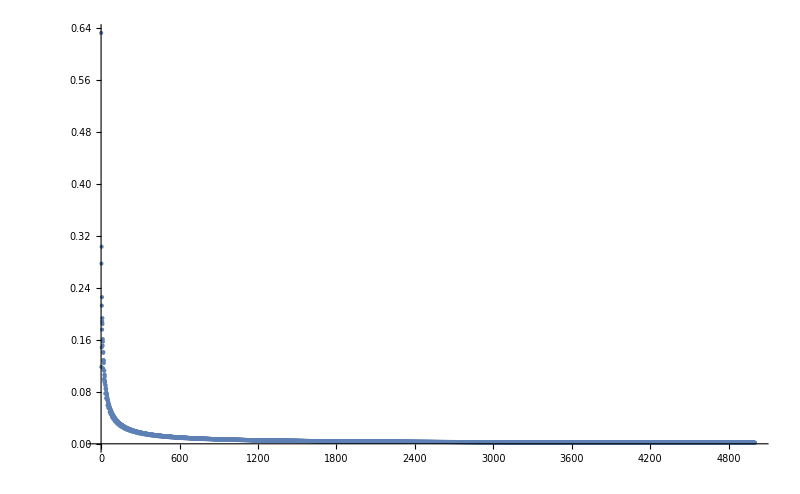

```mathematica
ListPlot[lces[[All,1]],ImageSize->800,PlotRange->All]
```

```mathematica
Clear[B,n,A,Jini,data,data1,data2,plot1,plot2,val];
A=10.0;
(*Jini=RandomPoint[Sphere[],1][[1]]*)
Jini={0.45,-0.7,Sqrt[1-0.45^2-0.7^2]};
data=ParallelTable[jmas[Jini,A,i],{i,1,2000}];
(*data=DeleteCases[data,Indeterminate];
data=DeleteCases[data,-∞];
data=Re[data];*)
```

General::munfl: 1/(9.93833×10^307) is too small to represent as a normalized machine number; precision may be lost.

Indeterminate

1.46129

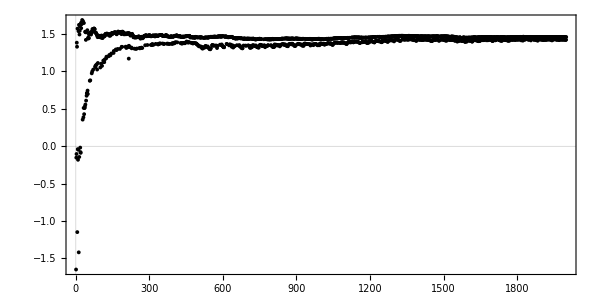

```mathematica
Mean[data]
jmas[Jini,A,2000]
plot=ListPlot[data,PlotTheme->"Scientific",PlotStyle->Black,ImageSize->600,AspectRatio->1/2,PlotRange->All]
```

```mathematica
mean={};
std={};
Do[
data1=data[[1;;i]];
AppendTo[mean,Mean[data1]];
AppendTo[std,StandardDeviation[data1]];
,{i,2,Length[data]}];
plot1=ListPlot[mean,PlotRange->All,PlotTheme->"Detailed",AspectRatio->1/2,ImageSize->600, PlotStyle->Blue];
plot2=ListPlot[std,PlotRange->All,PlotTheme->"Detailed",AspectRatio->1/2,ImageSize->600];
plot3=ListPlot[data,PlotRange->All,PlotTheme->"Detailed",AspectRatio->1/2,ImageSize->600,PlotStyle->Black];
```

0.0732628

0.0203099

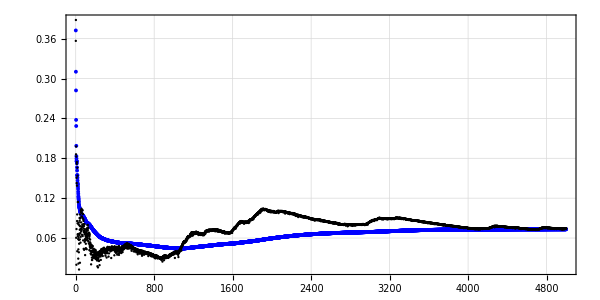

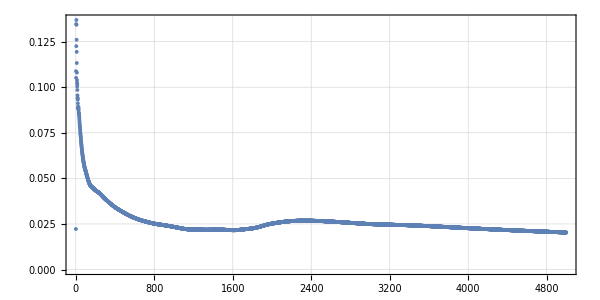

```mathematica
Mean[data]
StandardDeviation[data]
Show[plot1,plot3,PlotRange->All]
Show[plot2]
```

```mathematica
Clear[B,n,A,Jini,data,data1,data2,plot1,plot2,val];

movie={};
Do[
Jini={0.45,-0.7,Sqrt[1-0.45^2-0.7^2]};
data=ParallelTable[jmas[Jini,j,i],{i,1,5000}];
plot=ListPlot[data,PlotTheme->"Scientific",PlotStyle->Black,ImageSize->700,AspectRatio->1/2,PlotRange->All];
AppendTo[movie,plot];
,{j,0.0,10.0,0.2}];

ListAnimate[movie,AnimationRunning->False]
```

```mathematica
ListAnimate[movie,AnimationRunning->False]
```

```mathematica
Clear[n,Jini,data,plot1,val];
(*val=Flatten[{Range[1.0,10.0,0.01],Range[10.0,100.0,0.1]}];*)
val=Range[1.0,3.0,N[Pi/500]];
(*val=Range[0,100];*)
Jini={0.45,-0.7,Sqrt[1-0.45^2-0.7^2]};

lista={};
Do[
a=val[[j]];
data=ParallelTable[jmas[Jini,a,i],{i,900,1100}];
(*data=DeleteCases[data,Indeterminate];
data=DeleteCases[data,-∞];
data=Re[data];*)
AppendTo[lista,{a,Mean[data]}];

,{j,1,Length[val]}];
```

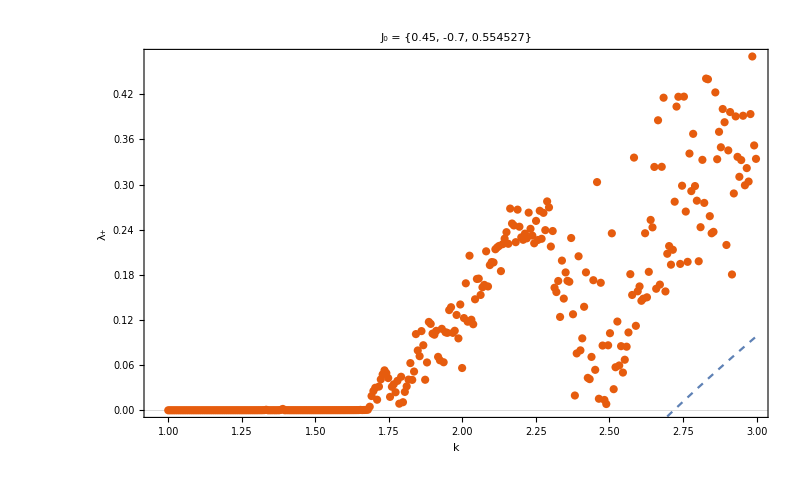

```mathematica
plot1=ListPlot[lista,PlotRange->All,PlotTheme->"Scientific",Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["k",40],Style["λ_+",40]},PlotLabel->Style["J_0 = "<>ToString[Jini],30], ImageSize->800];
plot2=Plot[Log[x*Sin[Pi/2]]-1,{x,1,3},PlotStyle->Dashed];
Show[plot1,plot2]
```

### Largest Lyapunov exponent

```mathematica
Clear[n,val,Jini,data,plot1,Qi,Ji];
n=1000;
(*val=Flatten[{Range[1.0,10.0,N[Pi/200]],Range[10.0,100.0,N[Pi/10]]}];*)
val=Range[1.0,100.0,N[Pi/50]];
Ji={0.45,-0.7,Sqrt[1-0.45^2-0.7^2]};
(*Qi={-0.15,-1.4};
Ji={Qi[[1]]*Sqrt[1-(1/4)Norm[Qi]^2],-Qi[[2]]*Sqrt[1-(1/4)Norm[Qi]^2],(1/2)Norm[Qi]^2 -1};*)
data=ParallelTable[{i,jmas[Ji,i,n]//Quiet},{i,val}];
```

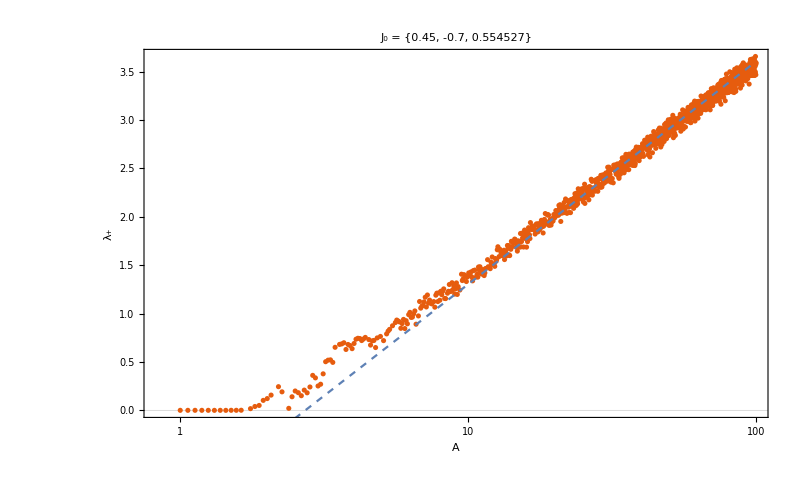

```mathematica
plot1=ListLogLinearPlot[data,PlotRange->All,PlotTheme->"Scientific",Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["A",40],Style["λ_+",40]},PlotLabel->Style["J_0 = "<>ToString[Ji],30], ImageSize->800];
plot2=LogLinearPlot[Log[x*Sin[Pi/2]]-1,{x,1.0,100.0},PlotRange->All,PlotStyle->Dashed];
Show[plot1,plot2]
```

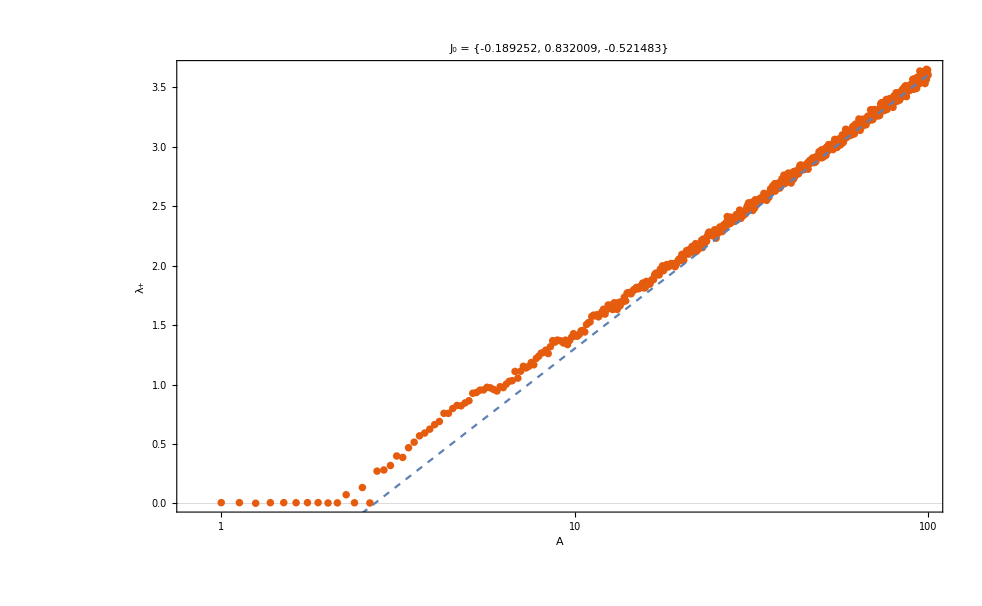

```mathematica
Clear[val,Ji,data2,plot1,plot2];
val=Range[1.0,100.0,N[Pi/25]];
(*val=Flatten[{Range[1.0,10.0,N[Pi/200]],Range[10.0,100.0,N[Pi/20]]}];*)
(*Ji={0.45,-0.7,Sqrt[1-0.45^2-0.7^2]};*)
Ji=RandomPoint[Sphere[],1][[1]];
n=5000;
(*tras=4000*)
data2=ParallelTable[{i,jmas2[Ji,i,n]},{i,val}];
plot1=ListLogLinearPlot[data2,PlotRange->All,PlotTheme->"Scientific",Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["A",40],Style["λ_+",40]},PlotLabel->Style["J_0 = "<>ToString[Ji],30], ImageSize->800];
plot2=LogLinearPlot[Log[x*Sin[Pi/2]]-1,{x,1.0,100.0},PlotRange->All,PlotStyle->Dashed];
Show[plot1,plot2]
```

```mathematica
J1={0,0,1};
J2={0,-1,0};
J3={0,0,-1};
J4={0,1,0};
val=Range[0.0,N[7Pi],N[Pi/200]];
data=ParallelTable[{i/Pi,jmas[J4,i,2000]},{i,val}];
```

General::munfl: 2.02827×10^307 (-1.02132546701733×10^-324) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.51346×10^307 (-3.18003048289904×10^-325) is too small to represent as a normalized machine number; precision may be lost.

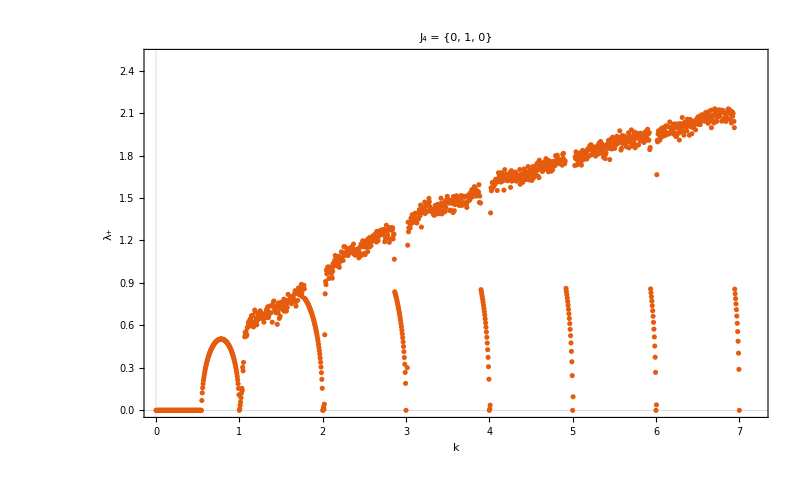

```mathematica
ListPlot[data,PlotRange->{{0,7.2},{0,2.5}},PlotTheme->"Scientific",Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["k",40],Style["λ_+",40]},PlotLabel->Style["J_4 = "<>ToString[J4],30], ImageSize->800]
```

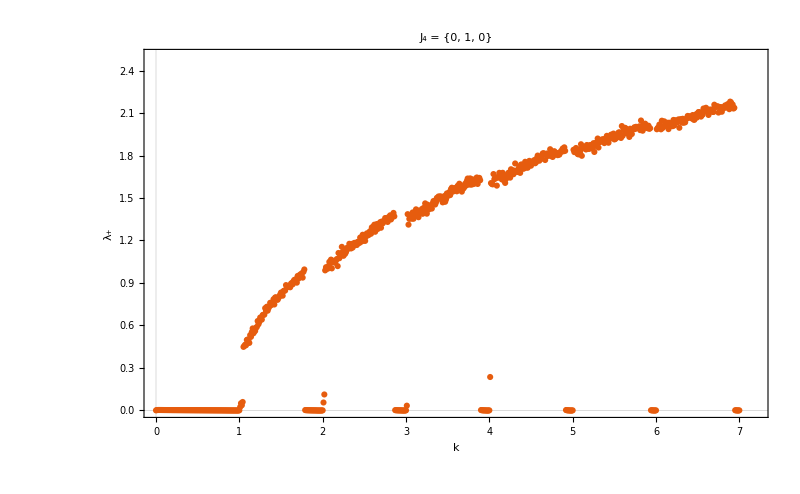

```mathematica
J1={0,0,1};
J2={0,-1,0};
J3={0,0,-1};
J4={0,1,0};
val=Range[0.0,N[7Pi],N[Pi/100]];
data=ParallelTable[{i/Pi,jmas2[J4,i,5000]},{i,val}];
ListPlot[data,PlotRange->{{0,7.2},{0,2.5}},PlotTheme->"Scientific",Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["k",40],Style["λ_+",40]},PlotLabel->Style["J_4 = "<>ToString[J4],30], ImageSize->800]
```

### Time Lyapunov exponent

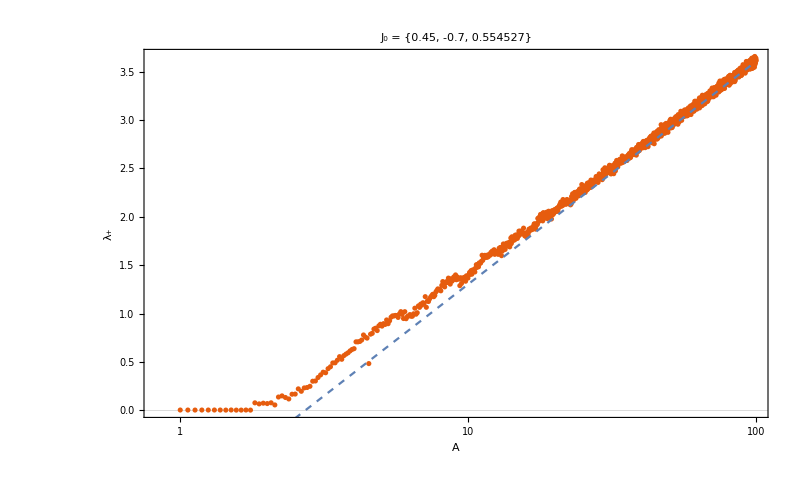

```mathematica
val=Flatten[{Range[1.0,10.0,N[Pi/200]],Range[10.0,100.0,N[Pi/20]]}]//Length
```

1146

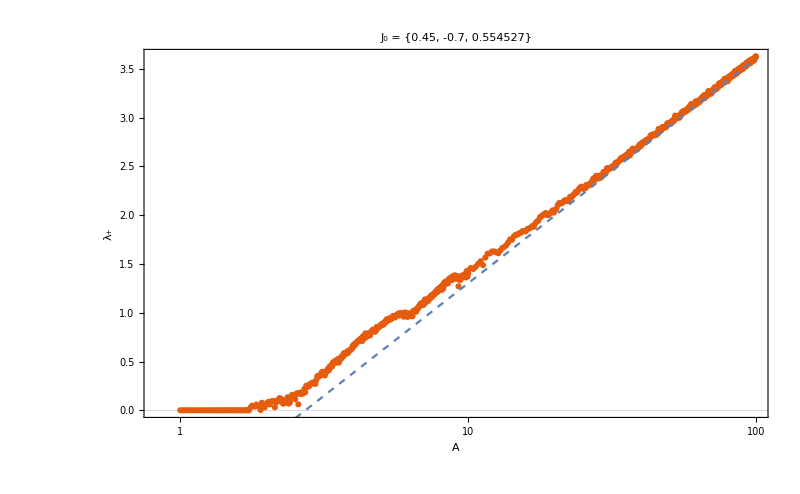

```mathematica
Clear[val,Ji,data2,plot1,plot2];
val=Flatten[{Range[1.0,10.0,N[Pi/150]],Range[10.0,100.0,N[Pi/15]]}];
(*val=Range[1.0,100.0,N[Pi/50]];*)
Ji={0.45,-0.7,Sqrt[1-0.45^2-0.7^2]};
n=10000;
(*tras=1000*)
data2=ParallelTable[{i,jmas2[Ji,i,n]},{i,val}];
plot1=ListLogLinearPlot[data2,PlotRange->All,PlotTheme->"Scientific",Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["A",40],Style["λ_+",40]},PlotLabel->Style["J_0 = "<>ToString[Ji],30], ImageSize->800];
plot2=LogLinearPlot[Log[x*Sin[Pi/2]]-1,{x,1.0,100.0},PlotRange->All,PlotStyle->Dashed];
Show[plot1,plot2]
```

## Variables Q,P mapeo 1

### Definiciones

```mathematica
SetDirectory["C:\\Users\\Pruebas\\Documents\\animaciones"];
```

SetDirectory::cdir: Cannot set current directory to C:\Users\Pruebas\Documents\animaciones.

```mathematica
Clear[mapeoQP,M,jmas];

mapeoQP[Qini_List,A_Real,n_Integer]:=Module[{Qi=Qini,Ji,Jxnew,Jynew,Jznew,s,Q,Qnew,B=N[Pi/2]},

Q={};
AppendTo[Q,Qi];
Ji={Qi[[1]]*Sqrt[1-(1/4)Norm[Qi]^2],-Qi[[2]]*Sqrt[1-(1/4)Norm[Qi]^2],(1/2)Norm[Qi]^2 -1};

Do[
Jznew=Ji[[2]]*N[Sin[B]]+Ji[[3]]*N[Cos[B]];
Jxnew=N[Ji[[1]]*N[Cos[A*Jznew]]-Ji[[2]]*N[Sin[A*Jznew]]*N[Cos[B]]+Ji[[3]]*N[Sin[A*Jznew]]*N[Sin[B]]];
Jynew=Ji[[1]]*N[Sin[A*Jznew]]-Ji[[2]]*N[Cos[A*Jznew]]*Cos[B]-Ji[[3]]*N[Cos[A*Jznew]]*N[Sin[B]];
Ji={Jxnew,Jynew,Jznew};

Qnew={Ji[[1]]*Sqrt[2/(1-Ji[[3]])],-Ji[[2]]*Sqrt[2/(1-Ji[[3]])]};
AppendTo[Q,Qnew];

,{i,1,n}];

Q

];


Jx[x_,y_,z_,A_,B_]:=N[x*Cos[A*(y*Sin[B]+z*Cos[B])]-y*Sin[A*(y*Sin[B]+z*Cos[B])]*Cos[B]+z*Sin[A*(y*Sin[B]+z*Cos[B])]*Sin[B]];
Jy[x_,y_,z_,A_,B_]:=N[x*Sin[A*(y*Sin[B]+z*Cos[B])]-y*Cos[A*(y*Sin[B]+z*Cos[B])]*Cos[B]-z*Cos[A*(y*Sin[B]+z*Cos[B])]*Sin[B]];
Jz[x_,y_,z_,A_,B_]:=N[y*Sin[B]+z*Cos[B]];

M[Jini_,A_Real,B_Real]:=Module[{M},
M={{D[Jx[x,y,z,A,B], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,A,B], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,A,B], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},
{D[Jy[x,y,z,A,B], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,A,B], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,A,B], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},{D[Jz[x,y,z,A,B], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,A,B], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,A,B], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}}}//N;
M
];

mapeoJ[Jini_,A_Real,n_Integer]:=Module[{Ji=Jini,J,Jxnew,Jynew,Jznew,B=N[Pi/2]},

J={};
AppendTo[J,Ji];

Do[
Jznew=Ji[[2]]*N[Sin[B]]+Ji[[3]]*N[Cos[B]];
Jxnew=N[Ji[[1]]*N[Cos[A*Jznew]]-Ji[[2]]*N[Sin[A*Jznew]]*N[Cos[B]]+Ji[[3]]*N[Sin[A*Jznew]]*N[Sin[B]]];
Jynew=Ji[[1]]*N[Sin[A*Jznew]]-Ji[[2]]*N[Cos[A*Jznew]]*Cos[B]-Ji[[3]]*N[Cos[A*Jznew]]*N[Sin[B]];
Ji={Jxnew,Jynew,Jznew};
AppendTo[J,Ji];

,{i,1,n}];

J

];

jmas[Jini_,A_Real,n_Integer]:=Module[{j,list=mapeoJ[N[Jini],N[A],n],data,B=N[Pi/2]},
data=Table[N[M[list[[i]],N[A],N[B]]],{i,1,n}];
j=N[Log[Max[N[Abs[N[Eigenvalues[N[Fold[Dot,data]]]]]]]^(N[1/n])]]

];
```

### Seccion de Poincare

```mathematica
Clear[Q0,A,B,n,poincare,plot,disco,Q1];
J0={0.45,-0.7,Sqrt[1-0.45^2-0.7^2]};
QJ0={J0[[1]]*Sqrt[2/(1-J0[[3]])],-J0[[2]]*Sqrt[2/(1-J0[[3]])]};
Q0=RandomPoint[Disk[{0,0},1.999],350];
B=Pi/2.;
A=1.82;
n=1000;

(*poincare=mapeoQP[Q0,A,B,n];*)
poincare=ParallelTable[mapeoQP[i,A,n]//Quiet,{i,Q0}];
```

```mathematica
plot=ListPlot[poincare,ImageSize->700,PlotTheme->"Scientific",PlotRange->All,AspectRatio->1,PlotStyle->PointSize[0.003],FrameLabel->{Style["Q",40],Style["P",40]}];
disco=Graphics[{Thick,Circle[{0,0},1.999]},AspectRatio->1];
punto=Graphics[{PointSize[0.03],Point[Q0]}];
Show[plot,disco,PlotRange->All]
```

-Graphics-

### Seccion de Poincare y proyeccion en t

```mathematica
Clear[J0,Q0,n,poincare,plot,disco,movie,d,array];
disco=Graphics[{Thick,Circle[{0,0},1.999]},AspectRatio->1];
J0={0.45,-0.7,Sqrt[1-0.45^2-0.7^2]};
QJ0={J0[[1]]*Sqrt[2/(1-J0[[3]])],-J0[[2]]*Sqrt[2/(1-J0[[3]])]};
(*J1={0,1,0};*)
(*QJ1={J1[[1]]*Sqrt[2/(1-J1[[3]])],-J1[[2]]*Sqrt[2/(1-J1[[3]])]};*)
(*Q0=RandomPoint[Disk[{0,0},1.99999],100];*)

d=0.2;
array=Table[{i,j},{i,-2.0,2.0,d},{j,-2.0,2.0,d}];
array=ArrayReshape[array,{Length[array]^2,2}];
Q0={};
Do[
If[Norm[array[[i]]]<=1.9999,AppendTo[Q0,array[[i]]]];
,{i,1,Length[array]}];

n=2000;


movie={};
Do[

poincare=ParallelTable[mapeoQP[j,i,n]//Quiet,{j,Q0}];
(*poincare=mapeoQP[QJ0,i,B,n];*)
(*plot=ListPlot[poincare,ImageSize->800,PlotTheme->"Scientific",PlotRange->All,AspectRatio->1,PlotStyle->PointSize[0.003],AxesLabel->{"x","y"},PlotLabel->{Style["J_0="<>ToString[Q0],25],Style["A="<>ToString[i],25]}];*)
plot=ListPlot[poincare,ImageSize->800,PlotTheme->"Scientific",PlotRange->All,AspectRatio->1,PlotStyle->PointSize[0.003],FrameLabel->{"Q","P"},PlotLabel->Style["A="<>ToString[i],25]];
AppendTo[movie,Show[plot,disco,PlotRange->All]];

,{i,0.,N[3Pi],N[Pi/20]}];
```

```mathematica
ListAnimate[movie,AnimationRunning->False,AnimationRate->1]
```

```mathematica
ParallelDo[Export["QPpoincare"<>ToString[i]<>".jpg",movie[[i]]],{i,1,Length[movie]}]
```

### Seccion y Lyapunov

```mathematica
Clear[A,n,poincare,plot,disco];
disco=Graphics[{Thick,Circle[{0,0},1.999]},AspectRatio->1];
num=200;
Q0=RandomPoint[Disk[{0,0},1.9999],num];
A=N[(4/5)Pi];
n=3000;
poincare=ParallelTable[mapeoQP[i,A,n],{i,Q0}];
```

```mathematica
plot=ListPlot[poincare,ImageSize->700,PlotTheme->"Scientific",PlotRange->All,AspectRatio->1,PlotStyle->PointSize[0.003],FrameLabel->{Style["Q",40],Style["P",40]},PlotLabel->Style["A = "<>ToString[A],40],FrameTicksStyle->25];
Show[plot,disco,PlotRange->All]
```

```mathematica
Clear[array,n,Q0,d,lyapunov,seclya];
n=3000;

(*Distribucion cuadrada sobre el disco*)
d=0.025;
array=Table[{i,j},{i,-2.0,0.0,d},{j,-2.0,0.0,d}];
array=ArrayReshape[array,{Length[array]^2,2}];
Q0={};
Do[
If[Norm[array[[i]]]<=1.9999,AppendTo[Q0,array[[i]]]];
,{i,1,Length[array]}];

J0={};
Do[
AppendTo[J0,{Q0[[i,1]]*Sqrt[1-(1/4)Norm[Q0[[i]]]^2],-Q0[[i,2]]*Sqrt[1-(1/4)Norm[Q0[[i]]]^2],(1/2)Norm[Q0[[i]]]^2 -1}];
,{i,1,Length[Q0]}];

(*Distribucion sonbre la esfera*)
(*J0=Table[{N[Sin[i]*Cos[j]],N[Sin[i]*Sin[j]],N[Cos[i]]},{i,0,N[2Pi],Pi/50.},{j,0,N[Pi],Pi/100.}];
J0=ArrayReshape[J0,{Length[J0]^2,3}];*)
Q0={};
Do[
AppendTo[Q0,{J0[[i,1]]*Sqrt[2/(1-J0[[i,3]])]//Quiet,-J0[[i,2]]*Sqrt[2/(1-J0[[i,3]])]//Quiet}];
,{i,1,Length[J0]}];
```

```mathematica
lyapunov=ParallelTable[jmas2[i,A,n],{i,J0}];
seclya=Transpose[{Q0,lyapunov}];
seclya=ArrayReshape[seclya,{Length[Q0],3}];
```

```mathematica
(*ListPointPlot3D[seclya]*)
plot2=ListDensityPlot[seclya,PlotRange->All,PlotTheme->"Scientific",PlotLabel->Style["A = "<>ToString[A],40],FrameLabel->{Style["Q",40],Style["P",40]},AspectRatio->1,ImageSize->700,ColorFunction->"TemperatureMap", InterpolationOrder->3];
Show[plot2,disco,PlotRange->All]
(*plot3=ListContourPlot[seclya,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["A = "<>ToString[A],40],FrameLabel->{Style["Q",40],Style["P",40]},AspectRatio->1,ImageSize->700];
Show[plot3,disco,PlotRange->All]*)
```

```mathematica
plot=ListPlot[poincare,ImageSize->700,PlotTheme->"Scientific",PlotRange->{{-2,0},{-2,0}},AspectRatio->1,PlotStyle->PointSize[0.003],FrameLabel->{Style["Q",40],Style["P",40]},PlotLabel->Style["A = "<>ToString[A],40],FrameTicksStyle->25,PlotStyle->Black];
plot2=ListDensityPlot[seclya,PlotRange->All,PlotTheme->"Scientific",PlotLabel->Style["A = "<>ToString[A],40],FrameLabel->{Style["Q",40],Style["P",40]},AspectRatio->1,ImageSize->700,ColorFunction->"TemperatureMap",InterpolationOrder->2];
Show[plot2,plot,disco,PlotRange->{{-2,0},{-2,0}}]
```

### graficas

-Graphics-

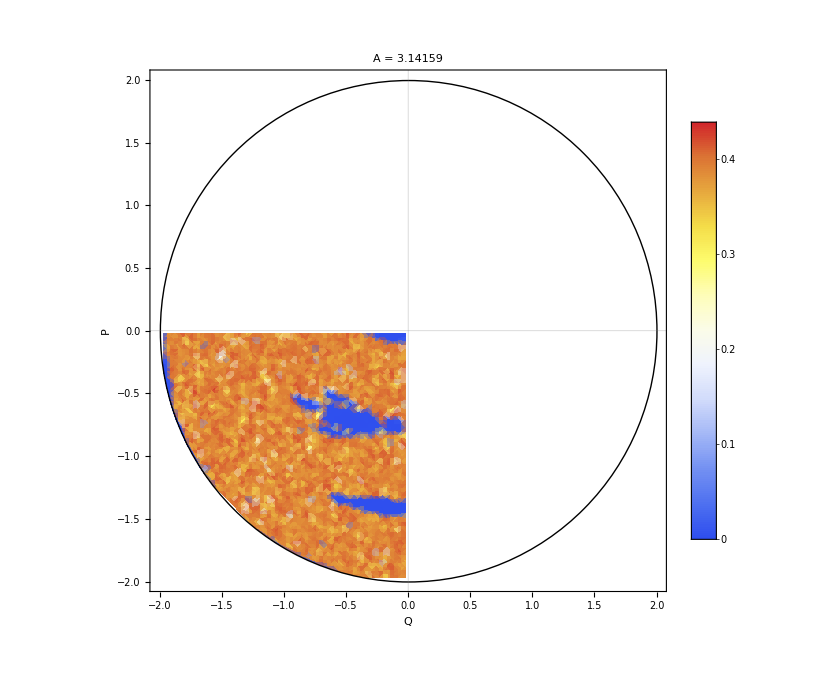

-Graphics-

## Kicked rotor

### Definiciones

```mathematica
Clear[mapeoQ,M,jmasR,Jx,Jy];

mapeoQ[Qini_,k_Real,n_Integer]:=Module[{Qi=Qini,Q,qnew,pnew},
Do[
pnew=N[Qi[[2]]+k*Sin[Qi[[1]]]];
qnew=N[Qi[[1]]+pnew];
Qi={qnew,pnew};
(*Qi={Mod[qnew,2Pi],Mod[pnew,2Pi]};*)
,{i,1,n}];

Qi

];

mapeoQ2[Qini_,k_Real,n_Integer]:=Module[{Qi=Qini,Q,qnew,pnew},
Q={};
AppendTo[Q,Qi];
Do[
pnew=N[Qi[[2]]+k*Sin[Qi[[1]]]];
qnew=N[Qi[[1]]+pnew];
Qi={qnew,pnew};
(*Qi={Mod[qnew,2Pi],Mod[pnew,2Pi]};*)
AppendTo[Q,Qi];
,{i,1,n}];
Q

];


Jx[q_,p_,k_]:=q+(p+k*Sin[q]);
Jy[q_,p_,k_]:=p+k*Sin[q];

M[Jini_,k_Real]:=Module[{M},
M={{D[Jx[q,p,k], q]/.{q->Jini[[1]],p->Jini[[2]]},D[Jx[q,p,k], p]/.{q->Jini[[1]],p->Jini[[2]]}},
{D[Jy[q,p,k], q]/.{q->Jini[[1]],p->Jini[[2]]},D[Jy[q,p,k], p]/.{q->Jini[[1]],p->Jini[[2]]}}}//N;
M
];

(*M[Jini_,k_]:=M[Jini,k]=Module[{M},
M={{1+k*Cos[Jini[[1]]],1},{k*Cos[Jini[[1]]],1}};
M
];
*)

jmasR[qini_,k_Real,n_Integer]:=Module[{j,list=mapeoQ2[qini,k,n],data},
data=Table[M[list[[i]],k]//N,{i,1,n+1}];
j=Log[Max[Eigenvalues[Fold[Dot,data]//N]//Re]^(1/n)]//N
];

jmas[qini_,k_Real,n_Integer]:=Module[{xt,q,r,s,lces,tras=5000},
xt=mapeoQ[N[qini],k,tras];
{q,r}=QRDecomposition[M[xt,k]];
s={};

Do[
xt=mapeoQ[xt,k,1];
{q,r}=QRDecomposition[M[xt,k].Transpose[q]];
(*s=Append[s,Table[r[[i,i]],{i,2}]];*)
s=Append[s,r[[1,1]]];

,{n}];

lces=Rest[FoldList[Plus,0,Re[Log[s]]]]/Range[n];
lces=lces[[1000;;n]];
Mean[lces]
];
```

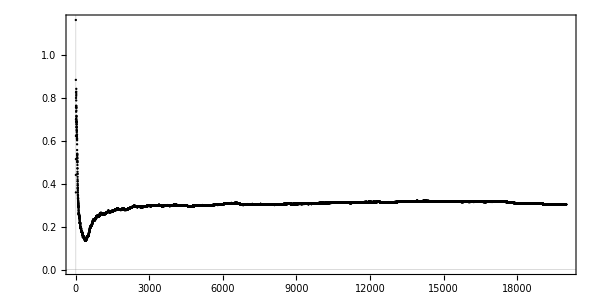

```mathematica
Clear[n,val,qini,data,plot1];
n=20000;
k=1.5;
qini={RandomReal[{-1,-1}],RandomReal[{-1,-1}]};
data=jmas[qini,k,n];

ListPlot[data,PlotRange->All,AspectRatio->1/2,PlotTheme->"Scientific",PlotStyle->Black,ImageSize->600]
```

### Seccion de Poincare

```mathematica
Clear[n,k,poincare,num];
n=5000;
num=100;
qini=Table[{RandomReal[{0,2Pi}],0},{i,num}];
(*qini={1,0};*)

(*k=0;
poincare=ParallelTable[mapeoQ[i,k,n],{i,qini}];
ListPlot[poincare,ImageSize->600,PlotTheme->"Scientific", ImageSize->700,Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["Q",30],Style["P",30]},PlotLabel->{Style["k="<>ToString[k],25],Style["n="<>ToString[n],25]},PlotRange->{{0,2Pi},{0,2Pi}},AspectRatio->1, ImageSize->800]*)

(*k=0.5;
poincare=ParallelTable[mapeoQ[i,k,n],{i,qini}];
ListPlot[poincare,ImageSize->600,PlotTheme->"Scientific", ImageSize->700,Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["Q",30],Style["P",30]},PlotLabel->{Style["k="<>ToString[k],25],Style["n="<>ToString[n],25]},PlotRange->{{0,2Pi},{0,2Pi}},AspectRatio->1, ImageSize->800]*)

(*k=1;
poincare=ParallelTable[mapeoQ[i,k,n],{i,qini}];
ListPlot[poincare,ImageSize->600,PlotTheme->"Scientific", ImageSize->700,Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["Q",30],Style["P",30]},PlotLabel->{Style["k="<>ToString[k],25],Style["n="<>ToString[n],25]},PlotRange->{{0,2Pi},{0,2Pi}},AspectRatio->1, ImageSize->800]*)

k=3.0;
poincare=ParallelTable[mapeoQ2[i,k,n],{i,qini}];
(*poincare=mapeoQ[qini,k,n];*)
ListPlot[poincare,ImageSize->600,PlotTheme->"Scientific", ImageSize->700,Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["Q",30],Style["P",30]},PlotLabel->{Style["k="<>ToString[k],25],Style["n="<>ToString[n],25]},PlotRange->All,AspectRatio->1, ImageSize->800]
```

-Graphics-

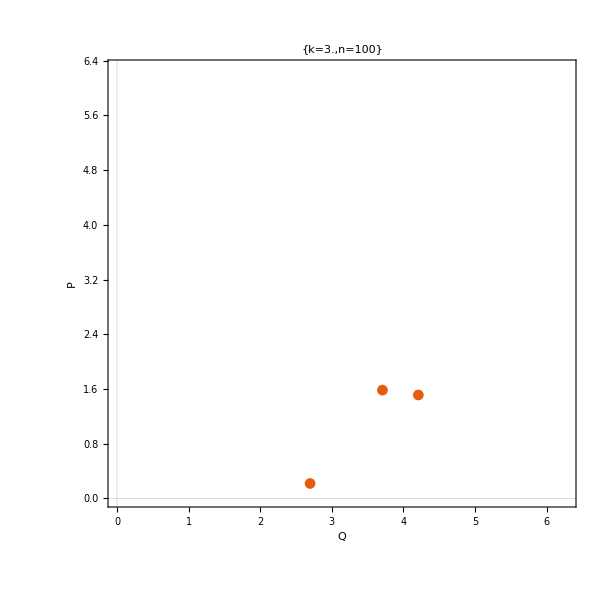

```mathematica
poincare=ParallelTable[mapeoQ2[i,k,4],{i,qini}];
(*poincare=mapeoQ[qini,k,n];*)
ListPlot[poincare,ImageSize->600,PlotTheme->"Scientific", ImageSize->700,Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["Q",30],Style["P",30]},PlotLabel->{Style["k="<>ToString[k],25],Style["n="<>ToString[n],25]},PlotRange->{{0,2Pi},{0,2Pi}},AspectRatio->1, ImageSize->800]
```

```mathematica
poincare//Dimensions
```

{25,1001,2}

```mathematica
Clear[n,k,poincare,num,movie,frame];
n=4000;
num=100;
qini=Table[{RandomReal[{0,2Pi}],RandomReal[{0,2Pi}]},{i,num}];

movie={};
val=Range[0.0,2,0.1];
Do[
poincare=ParallelTable[mapeoQ2[i,j,n],{i,qini}];
frame=ListPlot[poincare,ImageSize->600,PlotTheme->"Scientific", ImageSize->700,Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["Q",30],Style["P",30]},PlotLabel->{Style["k="<>ToString[j],25],Style["n="<>ToString[n],25]},PlotRange->{{0,2Pi},{0,2Pi}},AspectRatio->1, ImageSize->800];
AppendTo[movie,frame];
,{j,val}];
```

```mathematica
ListAnimate[movie,AnimationRunning->False,AnimationRate->1]
```

### Lyapunov exponent

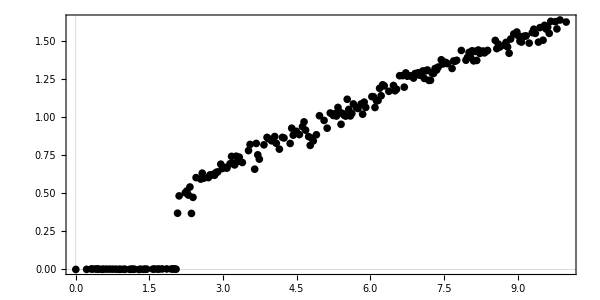

```mathematica
Clear[n,val,qini,data,plot1];
n=2000;
val=Range[0.0,10,N[Pi/100]];
qini={RandomReal[{0,2Pi}],RandomReal[{0,2Pi}]};
data=ParallelTable[{i,jmasR[qini,i,n]},{i,val}];
ListPlot[data,PlotRange->All,AspectRatio->1/2,PlotTheme->"Scientific",PlotStyle->Black,ImageSize->600]
```

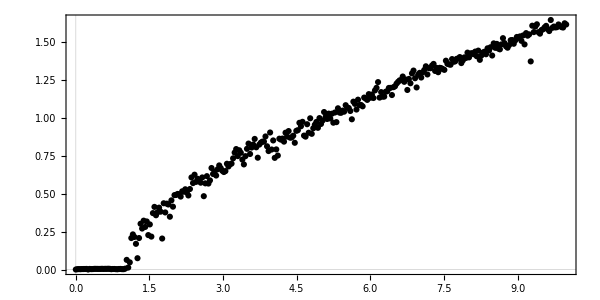

```mathematica
Clear[n,val,qini,data,plot1];
n=2000;
val=Range[0.0,10,N[Pi/100]];
qini={RandomReal[{0,2Pi}],RandomReal[{0,2Pi}]};
data=ParallelTable[{i,jmas[qini,i,n]},{i,val}];
ListPlot[data,PlotRange->All,AspectRatio->1/2,PlotTheme->"Scientific",PlotStyle->Black,ImageSize->600]
```

### Lyapunov y Poincare

```mathematica
Clear[qini,d,n,k,poincare,plot1,plot2];
n=2000;
d=0.5;
qini=Table[{i,j},{i,0.0,N[2Pi],d},{j,0.0,N[2Pi],d}];
qini=ArrayReshape[qini,{Length[qini]^2,2}];
k=N[(1/3)Pi];
poincare=ParallelTable[mapeoQ2[i,k,n],{i,qini}];
d=0.05;
qini=Table[{i,j},{i,0.0,N[2Pi],d},{j,0.0,N[2Pi],d}];
qini=ArrayReshape[qini,{Length[qini]^2,2}];
lyapunov=ParallelTable[jmas[i,k,n],{i,qini}];
seclya=Transpose[{qini,lyapunov}];
seclya=ArrayReshape[seclya,{Length[qini],3}];
```

```mathematica
plot1=ListPlot[poincare,ImageSize->600,PlotTheme->"Scientific", ImageSize->700,Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["Q",30],Style["P",30]},PlotLabel->{Style["k="<>ToString[k],25],Style["n="<>ToString[n],25]},PlotRange->{{0,2Pi},{0,2Pi}},AspectRatio->1, ImageSize->800]
plot2=ListDensityPlot[seclya,PlotRange->All,PlotTheme->"Scientific",PlotLabel->Style["k = "<>ToString[k],40],FrameLabel->{Style["Q",40],Style["P",40]},AspectRatio->1,ImageSize->700,ColorFunction->"TemperatureMap",InterpolationOrder->2]
(*plot3=Show[plot1,plot2]*)
```

-Graphics-

-Graphics-

```mathematica
plot3=Show[plot2,plot1]
```

-Graphics-

```mathematica
plot2=ListDensityPlot[seclya,PlotRange->All,PlotTheme->"Scientific",PlotLabel->Style["k = "<>ToString[k],40],FrameLabel->{Style["Q",40],Style["P",40]},AspectRatio->1,ImageSize->700,ColorFunction->"TemperatureMap"]
```

-Graphics-